## The Time Series

#### Time Series Plots

```mathematica
Manipulate[
Plot[
Cos[ω0 t+Γ Cos[ω1 t+ϕ1]],
{t,0,(12π)/(ω0 ω1)},
Ticks->None,
AxesLabel->{"Time"}
],
{{Γ,3},0,15},
{{ω0,0.42},0,15},
{{ω1,0.46},0,10},
{{ϕ1,0.1},0,2π}
]
```

## The Fourier Transform

### The Fourier Transform -- Plotted

#### The Complex Function

```mathematica
Manipulate[
Show[
ListPlot[
Table[{ω0+n ω1,N[Abs[BesselJ[n,Γ]]^2]},{n,-10,10}],
Filling->Axis,
PlotRange->{{-60,60},{-0.02,1.02}},
AxesLabel->{"","Power in Sideband Relative to Carrier Frequency"}]

],
{{ω0,6 √2},0,10},
{{ω1,5},0,10},
{Γ,0,15}
]
```

#### The Real Function

-There is no extra information in the negative frequencies

```mathematica
Manipulate[
Show[
ListPlot[
Table[{ω0+n ω1,N[Abs[BesselJ[n,Γ]]^2]},{n,-10,10}],
Filling->Axis,
PlotRange->{{-1.02(10ω1+ω0),1.02(10ω1+ω0)},{0,1.02}},
AxesLabel->{"","Power in Sideband Relative to Carrier Frequency"}],
ListPlot[
Table[{-ω0+n ω1,N[Abs[BesselJ[n,Γ]]^2]},{n,-10,10}],
Filling->Axis,
PlotRange->{{-1.02(10ω1+ω0),1.02(10ω1+ω0)},{0,1.02}},
PlotStyle->Red,
AxesLabel->{"","Power in Sideband Relative to Carrier Frequency"}]

],
{{ω0,6 √2},0,10},
{{ω1,5},0,10},
{Γ,0,15}
]
```

```mathematica
Module[{ω0=10.0,ω1=3.69,Γ=1.75,Vecs},
Vecs=Table[Arrow[{{ω0+n ω1,0,0},{ω0+n ω1,30BesselJ[n,Γ]Sin[(n π)/2],30BesselJ[n,Γ]Cos[(n π)/2]}}],{n,-7,7}];
Show[
Graphics3D[Vecs,ImageSize->600],
ParametricPlot3D[{0,10Sin[θ],10Cos[θ]},{θ,0,2π}],
ParametricPlot3D[{z,0,0},{z,ω0-7ω1,ω0+7ω1}],
ParametricPlot3D[{{0,x,0},{0,0,x}},{x,-12,12}]
]
]
```

-Graphics3D-

```mathematica
point[Γ_,ϕ1_,m_]:=BesselJ[m,Γ]{Cos[m (ϕ1+π/2)],Sin[m (ϕ1+π/2)]};
Manipulate[
Grid[{{
Graphics[{
{Red,Thick, Arrow[{{0,0},{BesselJ[0,Γ],0}}]},
Table[
Arrow[{{0,0},point[Γ,ϕ1,m]}],
{m,1,40}
],
Table[
Arrow[{{0,0},point[Γ,ϕ1,-m]}],
{m,1,40}
]},
PlotRange->{{-1,1},{-1,1}},
ImageSize->400,
Axes->True],
Plot[Cos[ω0 t+Γ Cos[ω1 t +ϕ1]],{t,0,4π},ImageSize->400]
}}],
{Γ,0,50},
{{ω0,0.46},0,2π},
{{ω1,0.42},0,2π},
{ϕ1,0,2π}
]
```

```mathematica
J[n_,x_]:=BesselJ[n,x];
point[Γ_,ϕ1_,m_]:=J[m,Γ]{Cos[m (ϕ1+π/2)],Sin[m (ϕ1+π/2)]};

Manipulate[
pointArray=Table[∑_(m=1)^n (point[Γ,ϕ1,(-1)^m Floor[m/2]]),{n,1,21}];
Vecs={
{Red,Thick,Arrow[{{0,0},{J[0,Γ],0}}]},
Arrow[{{J[0,Γ],0},pointArray[[1]]}],
Table[
Arrow[{pointArray[[n]],pointArray[[n+1]]}],
{n,1,20}]};

Grid[{{
Show[
PolarPlot[1,{θ,0,2π},ImageSize->400],
Graphics[
{
Vecs
},
PlotRange->{{-1,1},{-1,1}},
ImageSize->300,
Axes->True]
],
Plot[Cos[ω0 t+Γ Cos[ω1 t +ϕ1]],{t,0,4π},ImageSize->400]
}}],
{{Γ,5.2},0,50},
{{ω0,0.46},0,2π},
{{ω1,0.42},0,2π},
{ϕ1,0,2π}
]
```

```mathematica
J[n_,x_]:=BesselJ[n,x];
gustafsonPoint[Γ_,ΓX_,ϕ1_,m_]:=J[m,Γ]J[m,ΓX]{Cos[m (ϕ1+π/2)],Sin[m (ϕ1+π/2)]};

Manipulate[
pointArray=Table[∑_(m=1)^n (gustafsonPoint[Γ,ΓX,ϕ1,(-1)^m Floor[m/2]]),{n,1,31}];
Vecs={
Arrow[{{0,0},{J[0,Γ],0}}],
Arrow[{{J[0,Γ],0},pointArray[[1]]}],
Table[
Arrow[{pointArray[[n]],pointArray[[n+1]]}],
{n,1,20}]};

Graphics[Vecs,
PlotRange->{{-1,1},{-1,1}},
ImageSize->300,
Axes->True],
{ΓX,0,50},
{Γ,0,50},
{ω0,0,2π},
{ω1,0,2π},
{ϕ1,0,2π}
]
```

### Plot the Xcode output

#### Calculating a single value array

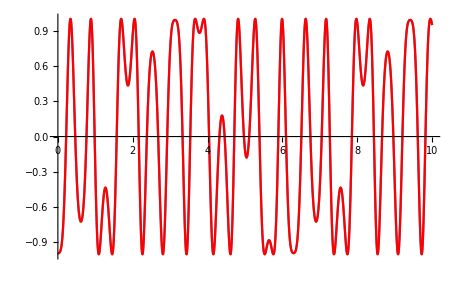

```mathematica
(*pathToSolution=FileNameJoin[{NotebookDirectory[],"dataOut/solutionMatrix.csv"}];*)
Module[{n=10000,t1=10.0,Γ=3.0,ω0=1.0,ω1=5.0,pathToSolution,solution},
pathToSolution="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out.csv";
solution=Import[pathToSolution,"Table"];
(*Export["/Volumes/userFilesPartition/Users/curtisrau/Desktop/BesselJ4.png",*)
Show[
Plot[Cos[ω0 t+Γ Cos[ω1 t]],{t,0,t1}],
ListLinePlot[solution,DataRange->{0,t1},PlotRange->All,ImageSize->500,PlotStyle->Red]]
]
```

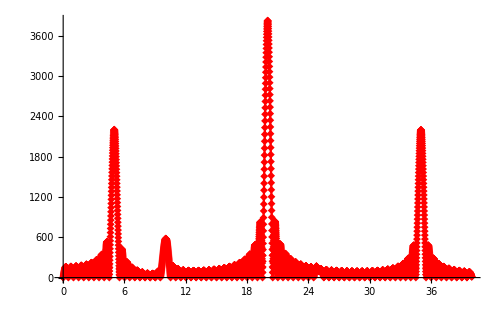

```mathematica
(*pathToSolution=FileNameJoin[{NotebookDirectory[],"dataOut/solutionMatrix.csv"}];*)
Module[{n=10000,df=0.01,tMin=0,tMax=50,Γ=3.0,ω0=1.0,ω1=5.0,pathToSolution,solution},
pathToSolution="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out.csv";
solution=Flatten[Import[pathToSolution,"Table"]];
(*Export["/Volumes/userFilesPartition/Users/curtisrau/Desktop/BesselJ4.png",*)
Show[
(*Plot[Cos[ω0 t+Γ Cos[ω1 t]],{t,0,t1}],*)
ListLinePlot[Table[solution[[i]],{i,0,4000}],DataRange->{0,4000*df},PlotRange->All,ImageSize->500,PlotStyle->Red,PlotMarkers->{"◆", 8}]
]
]
```

#### Steps in omega0

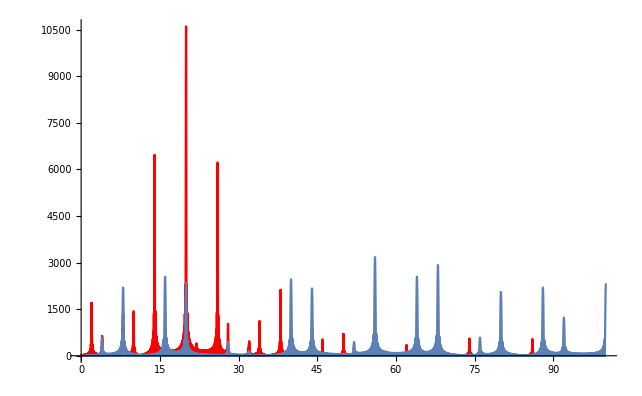

```mathematica
Module[{pathToSolution,solution,pathToSolution2,solution2},
pathToSolution="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out.csv";
solution=Flatten[Import[pathToSolution,"Table"]];
pathToSolution2="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out2.csv";
solution2=Flatten[Import[pathToSolution2,"Table"]];
Show[
ListLinePlot[solution,PlotRange->All,ImageSize->500,PlotStyle->Red,DataRange->{0,20000*0.005}],
ListLinePlot[solution2,PlotRange->All,ImageSize->500,PlotRange->All,DataRange->{0,20000*0.005}]

]
]
```

```mathematica
Module[{pathToSolution,solution},
pathToSolution="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out3.csv";
solution=Import[pathToSolution,"Table"];
Export["/Volumes/userFilesPartition/Users/curtisrau/Desktop/BesselJn80.png",
Show[
Plot[BesselJ[n-1,100/4000 3200],{n,0,100},PlotRange->All,AxesLabel->{"n","J_n(80)"},ImageSize->800],
ListPlot[solution[[3200]],PlotRange->All,PlotStyle->Red]]
]
]
```

/Volumes/userFilesPartition/Users/curtisrau/Desktop/BesselJn80.png

#### Steps in Gamma

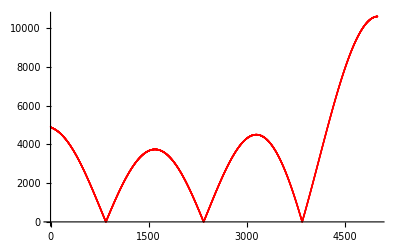

```mathematica
Module[{pathToSolution,solution},
pathToSolution="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out.csv";
solution=Flatten[Import[pathToSolution,"Table"]];
Show[
(*Plot[BesselJ[n-1,100/4000 3200],{n,0,100},PlotRange->All,AxesLabel->{"n","J_n(80)"},ImageSize->800],*)
ListPlot[solution,PlotRange->All,PlotStyle->Red]]
]
```

### Steps in phi1

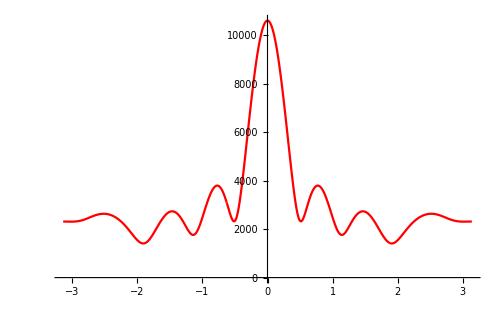

```mathematica
Module[{pathToSolution,solution,pathToSolution2,solution2},
pathToSolution="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out.csv";
solution=Flatten[Import[pathToSolution,"Table"]];
pathToSolution2="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out2.csv";
solution2=Flatten[Import[pathToSolution2,"Table"]];
Show[
ListLinePlot[solution,PlotRange->All,ImageSize->500,PlotStyle->Red,DataRange->{-π,π}](*,
ListLinePlot[solution2,PlotRange->All,ImageSize->500,PlotRange->All,DataRange->{0,20000*0.005}]*)

]
]
```

### Calculating a bessel at a single point using the integral

```mathematica
Manipulate[
Plot[Cos[π z*Sin[x]-(n)*x],{x,0,π}],
{n,0,10},
{z,0,10}
]
```

```mathematica
Floor[(2(π 2.5))/π]
```

5

## Determin How Many Sidebands Should be Included in the Search: What is the Value of “n” that Maximizes J_n(x)?

```mathematica
Plot3D[BesselJ[n-1,x],{n,1,20},{x,0,20},PlotRange->All,AxesLabel->{"N","X"}]
```

-Graphics3D-

### Plot of the n that maximizes J_n(x) as a function of x

n → Γ - Log_π(Γ)

#### How does it work for small x?

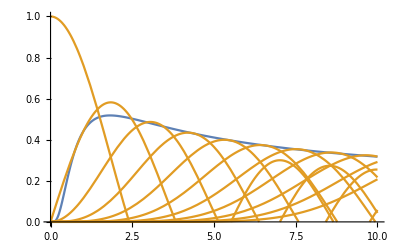

```mathematica
Plot[{
BesselJ[x-Log[π,x],x],
Table[BesselJ[n,x],{n,0,10}]
},{x,0,10},
PlotRange->{0,1}]
```

#### How does it work for large x?

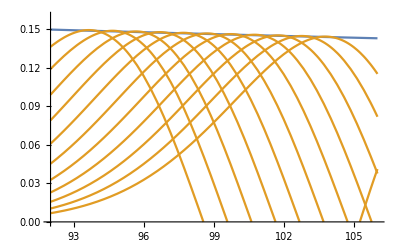

```mathematica
Plot[{
BesselJ[x-Log[π,x],x],
Table[BesselJ[n,x],{n,90,100}]
},{x,92,106},
PlotRange->{0,0.16}]
```

#### How well does it work?

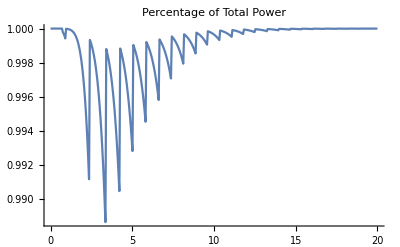
-Graphics-Modulation Index: Γ [rad]

```mathematica
partialSum[x_]:=Module[{N=Round[1.5(x-Log[π,x])]+1},∑_(n=-N)^N BesselJ[n,x]^2];
Labeled[
ListLinePlot[
Table[partialSum[x],{x,0,20,0.05}],
DataRange->{0,20},
PlotRange->All,
PlotLabel->"Percentage of Total Power"],
"Modulation Index: Γ [rad]"
]
```

## Results

#### No Noise, 10s of data

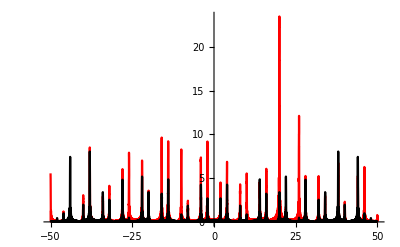

```mathematica
Module[{pathToSolution1,solution1,pathToSolution2,solution2,sampleRate=100},
nyquistF=0.5 * sampleRate;
pathToSolution1="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out.csv";
solution1=Flatten[Import[pathToSolution1,"Table"]];
pathToSolution2="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out2.csv";
solution2=Flatten[Import[pathToSolution2,"Table"]];
Show[
ListLinePlot[solution1,DataRange->{-nyquistF,nyquistF},PlotRange->All,PlotStyle->Red],
ListLinePlot[solution2,DataRange->{-nyquistF,nyquistF},PlotRange->All,PlotStyle->Black]
]
]
```

#### 10x Noise Level, 10s of data, 100Hz sample rate

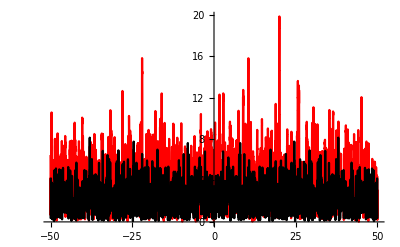

```mathematica
Module[{pathToSolution1,solution1,pathToSolution2,solution2,sampleRate=100},
nyquistF=0.5 * sampleRate;
pathToSolution1="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out.csv";
solution1=Flatten[Import[pathToSolution1,"Table"]];
pathToSolution2="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out2.csv";
solution2=Flatten[Import[pathToSolution2,"Table"]];
Show[
ListLinePlot[solution1,DataRange->{-nyquistF,nyquistF},PlotRange->All,PlotStyle->Red],
ListLinePlot[solution2,DataRange->{-nyquistF,nyquistF},PlotRange->All,PlotStyle->Black]
]
]
```

#### 10x Noise Level, 20s of data, 100Hz sample rate

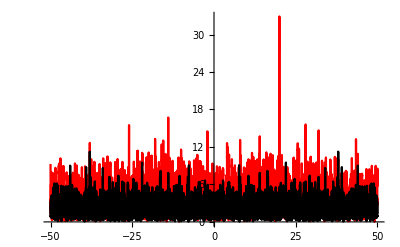

```mathematica
Module[{pathToSolution1,solution1,pathToSolution2,solution2,sampleRate=100},
nyquistF=0.5 * sampleRate;
pathToSolution1="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out.csv";
solution1=Flatten[Import[pathToSolution1,"Table"]];
pathToSolution2="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out2.csv";
solution2=Flatten[Import[pathToSolution2,"Table"]];
Show[
ListLinePlot[solution1,DataRange->{-nyquistF,nyquistF},PlotRange->All,PlotStyle->Red],
ListLinePlot[solution2,DataRange->{-nyquistF,nyquistF},PlotRange->All,PlotStyle->Black]
]
]
```

#### 10x Noise Level, 50s of data, 150 Hz sample rate

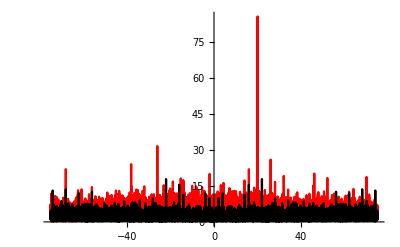

```mathematica
Module[{pathToSolution1,solution1,pathToSolution2,solution2,sampleRate=150},
nyquistF=0.5 * sampleRate;
pathToSolution1="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out.csv";
solution1=Flatten[Import[pathToSolution1,"Table"]];
pathToSolution2="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out2.csv";
solution2=Flatten[Import[pathToSolution2,"Table"]];
Show[
ListLinePlot[solution1,DataRange->{-nyquistF,nyquistF},PlotRange->All,PlotStyle->Red],
ListLinePlot[solution2,DataRange->{-nyquistF,nyquistF},PlotRange->All,PlotStyle->Black]
]
]
```

#### 10x Noise Level, 50s of data, 300 Hz sample rate

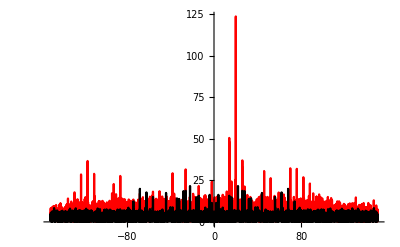

```mathematica
Module[{pathToSolution1,solution1,pathToSolution2,solution2,sampleRate=300},
nyquistF=0.5 * sampleRate;
pathToSolution1="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out.csv";
solution1=Flatten[Import[pathToSolution1,"Table"]];
pathToSolution2="/Volumes/userFilesPartition/Users/curtisrau/Desktop/out2.csv";
solution2=Flatten[Import[pathToSolution2,"Table"]];
Show[
ListLinePlot[solution1,DataRange->{-nyquistF,nyquistF},PlotRange->All,PlotStyle->Red],
ListLinePlot[solution2,DataRange->{-nyquistF,nyquistF},PlotRange->All,PlotStyle->Black]
]
]
```

## Xcode Output

### Using The Full Fourier Transform

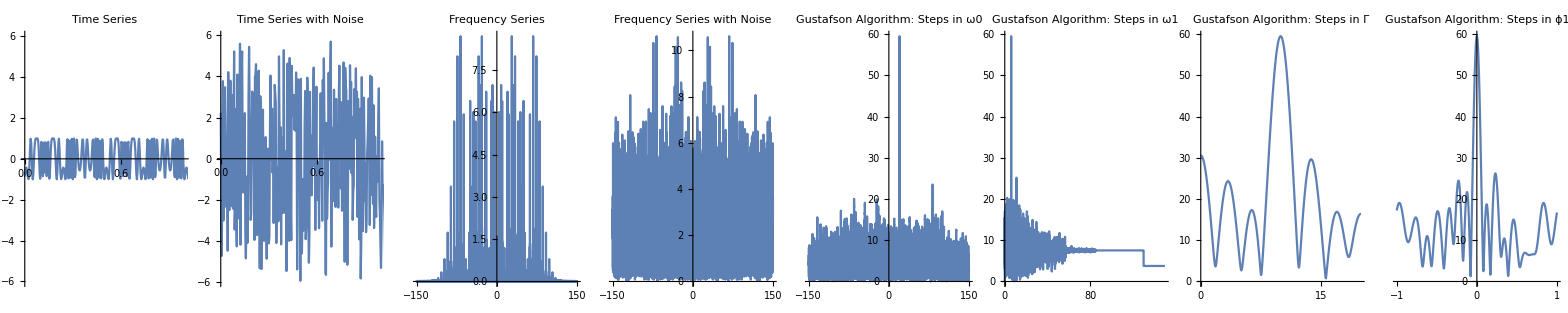

```mathematica
Module[{
pathTimeSeries,
timeSeries,
pathTimeSeriesNoise,
timeSeriesNoise,
pathFrequencySeries,
frequencySeries,
pathFrequencySeriesNoise,
frequencySeriesNoise,
pathOutOmega0,
outOmega0,
pathOutOmega1,
outOmega1,
pathOutGamma,
outGamma,
pathOutϕ1,
outϕ1,
sampleRate=300,
duration=10,
ΓMax=20,
nyquestFreq
},
nyquestFreq=sampleRate/2;
pathTimeSeries="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/timeSeries.csv";
timeSeries=Flatten[Import[pathTimeSeries,"Table"]];
pathTimeSeriesNoise="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/timeSeriesNoise.csv";
timeSeriesNoise=Flatten[Import[pathTimeSeriesNoise,"Table"]];
pathFrequencySeries="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/frequencySeries.csv";
frequencySeries=Flatten[Import[pathFrequencySeries,"Table"]];
pathFrequencySeriesNoise="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/frequencySeriesNoise.csv";
frequencySeriesNoise=Flatten[Import[pathFrequencySeriesNoise,"Table"]];
pathOutOmega0="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/outOmega0.csv";
outOmega0=Flatten[Import[pathOutOmega0,"Table"]];
pathOutOmega1="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/outOmega1.csv";
outOmega1=Flatten[Import[pathOutOmega1,"Table"]];
pathOutGamma="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/outGamma.csv";
outGamma=Flatten[Import[pathOutGamma,"Table"]];
pathOutϕ1="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/outPhi1.csv";
outϕ1=Flatten[Import[pathOutϕ1,"Table"]];
Grid[{{
ListLinePlot[timeSeries,DataRange->{0,duration},PlotRange->{{0,1},{-6,6}},PlotLabel->"Time Series", ImageSize->400],
ListLinePlot[timeSeriesNoise,DataRange->{0,duration},PlotRange->{{0,1},All},PlotLabel->"Time Series with Noise",ImageSize->400],
ListLinePlot[frequencySeries,DataRange->{-nyquestFreq,nyquestFreq},PlotLabel->"Frequency Series",PlotRange->All,ImageSize->400],
ListLinePlot[frequencySeriesNoise,DataRange->{-nyquestFreq,nyquestFreq},PlotLabel->"Frequency Series with Noise",PlotRange->All,ImageSize->400],
ListLinePlot[outOmega0,DataRange->{-nyquestFreq,nyquestFreq},PlotLabel->"Gustafson Algorithm: Steps in ω0",PlotRange->All,ImageSize->400],
ListLinePlot[outOmega1,DataRange->{0,nyquestFreq},PlotLabel->"Gustafson Algorithm: Steps in ω1",PlotRange->All,ImageSize->400],
ListLinePlot[outGamma,DataRange->{0,ΓMax},PlotLabel->"Gustafson Algorithm: Steps in Γ",PlotRange->All,ImageSize->400],
ListLinePlot[outϕ1,DataRange->{-1,1},PlotLabel->"Gustafson Algorithm: Steps in ϕ1",PlotRange->All,ImageSize->400]
}}]
]
```

### Using Only The Positive Frequencies

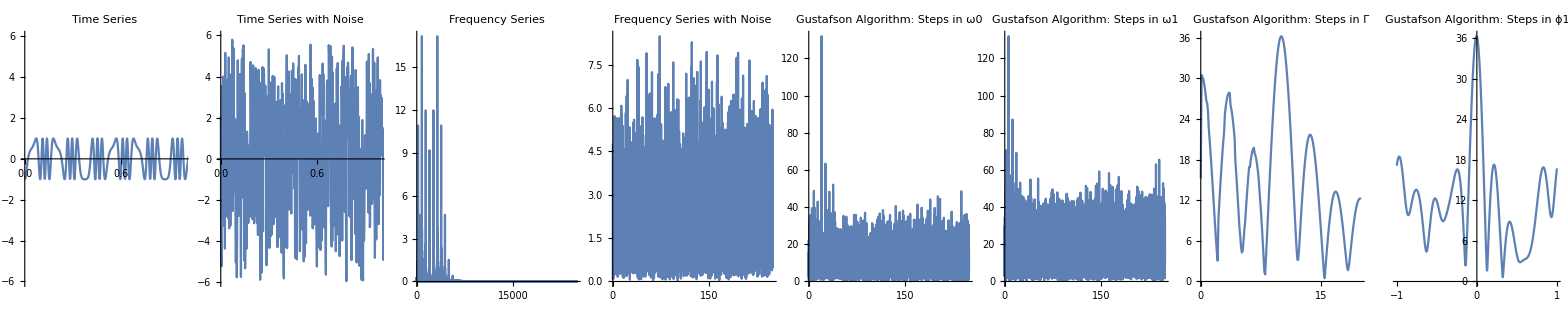

```mathematica
Module[{
pathTimeSeries,
timeSeries,
pathTimeSeriesNoise,
timeSeriesNoise,
pathFrequencySeries,
frequencySeries,
pathFrequencySeriesNoise,
frequencySeriesNoise,
pathOutOmega0,
outOmega0,
pathOutOmega1,
outOmega1,
pathOutGamma,
outGamma,
pathOutϕ1,
outϕ1,
sampleRate=500,
duration=10,
ΓMax=20,
nyquestFreq
},
nyquestFreq=sampleRate/2;
pathTimeSeries="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/timeSeries.csv";
timeSeries=Flatten[Import[pathTimeSeries,"Table"]];
pathTimeSeriesNoise="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/timeSeriesNoise.csv";
timeSeriesNoise=Flatten[Import[pathTimeSeriesNoise,"Table"]];
pathFrequencySeries="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/frequencySeries.csv";
frequencySeries=Flatten[Import[pathFrequencySeries,"Table"]];
pathFrequencySeriesNoise="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/frequencySeriesNoise.csv";
frequencySeriesNoise=Flatten[Import[pathFrequencySeriesNoise,"Table"]];
pathOutOmega0="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/outOmega0.csv";
outOmega0=Flatten[Import[pathOutOmega0,"Table"]];
pathOutOmega1="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/outOmega1.csv";
outOmega1=Flatten[Import[pathOutOmega1,"Table"]];
pathOutGamma="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/outGamma.csv";
outGamma=Flatten[Import[pathOutGamma,"Table"]];
pathOutϕ1="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/outPhi1.csv";
outϕ1=Flatten[Import[pathOutϕ1,"Table"]];
Grid[{{
ListLinePlot[timeSeries,DataRange->{0,duration},PlotRange->{{0,1},{-6,6}},PlotLabel->"Time Series", ImageSize->400],
ListLinePlot[timeSeriesNoise,DataRange->{0,duration},PlotRange->{{0,1},All},PlotLabel->"Time Series with Noise",ImageSize->400],
ListLinePlot[frequencySeries,(*DataRange->{0,nyquestFreq},*)PlotLabel->"Frequency Series",PlotRange->All,ImageSize->400],
ListLinePlot[frequencySeriesNoise,DataRange->{0,nyquestFreq},PlotLabel->"Frequency Series with Noise",PlotRange->All,ImageSize->400],
ListLinePlot[outOmega0,DataRange->{0,nyquestFreq},PlotLabel->"Gustafson Algorithm: Steps in ω0",PlotRange->All(*{{0,45},All}*),ImageSize->400],
ListLinePlot[outOmega1,DataRange->{0,nyquestFreq},PlotLabel->"Gustafson Algorithm: Steps in ω1",PlotRange->All(*{{0,45},All}*),ImageSize->400],
ListLinePlot[outGamma,DataRange->{0,ΓMax},PlotLabel->"Gustafson Algorithm: Steps in Γ",PlotRange->All,ImageSize->400],
ListLinePlot[outϕ1,DataRange->{-1,1},PlotLabel->"Gustafson Algorithm: Steps in ϕ1",PlotRange->All,ImageSize->400]
}}]
]
```

```mathematica
Module[{
outOmega,
pathOut,
sampleRate=500,
duration=10,
ΓMax=20,
nyquestFreq
},
nyquestFreq=sampleRate/2;
pathOut="/Volumes/userFilesPartition/Users/curtisrau/Desktop/output/outSearch.csv";
outOmega0=Import[pathOut,"Table"];
ListPlot3D[outOmega0,AxesLabel->{"Step in f0","Step in f1"},PlotRange->All]
]
```

-Graphics3D-

## Analysis

### Steps in Γ

```mathematica
Module[{Γ=10,dXmax=10},
ListPlot3D[
Table[∑_(n=-NN)^NN BesselJ[n,Γ]BesselJ[n,Γ+x],
{x,-dXmax,dXmax,0.1},{NN,0,20,2}],
DataRange->{{0,20},{-dXmax,dXmax}},
AxesLabel->{"Steps in N","Steps in Γ"},
ImageSize->500
]
]
```

-Graphics3D-

### Steps in ϕ_1

```mathematica
Module[{Γ=10,δϕ1max=π},
ListPlot3D[
Table[Abs[∑_(n=-NN)^NN Exp[I n (δϕ1(*+π/2*)) ] BesselJ[n,Γ]^2],
{δϕ1,-δϕ1max,δϕ1max,0.1},{NN,0,20,2}],
PlotRange->All,
DataRange->{{0,20},{-δϕ1max,δϕ1max}},
AxesLabel->{"Steps in N","Steps in ϕ1"},
ImageSize->500
]
]
```

-Graphics3D-

## Noise

Doing a 4 dimensional fourier transform using h_0 e^(I(ω_0 t + ϕ_0+Γ cos(ω_1 t + ϕ_1))) as the basis functions would take

T~N_t N_ω_0 N_Γ N_ω_1 N_ϕ_1

With this algorithm the time the computation takes goes as

T~N_t N_ω+N_ω_0 N_Γ N_ω_1 N_ϕ_1

Signal:Noise ratio is improved by using more points in the time series.  This is why the Gustafson Algorithm is useful.

## Miscellaneous

#### What is the max value Γ can take on?

```mathematica
(1.496 10^11)/(√((2.99792458 10^8)^2(*-(1.496 10^11)^2((2π)/(3.154 10^7))^2*)))//N
```

499.012

```mathematica
499.012(2π 5000)//N
```

1.56769×10^7

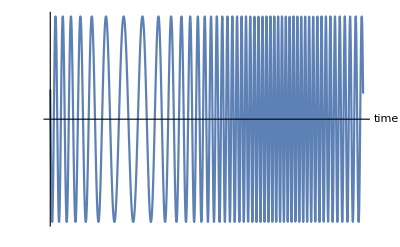

```mathematica
Module[{c=2.99792458*10^8,v=2 10^8(*2.9802*10^4*),ωe=1.992*10^-7,ω0=(2π)/(3600 24 10)},
γ[v_]:=1/(√(1-(v/c)^2));
β[v_]:=v/c;
Δ[β_]:=√((1-β)/(1+β));
Plot[{Cos[ω0 γ[v]t+ω0(γ[v]β[v])/ωe Cos[ωe t]]},{t,0,(2π)/ωe},
Ticks->None,
AxesLabel->{"time"}
]
]
```

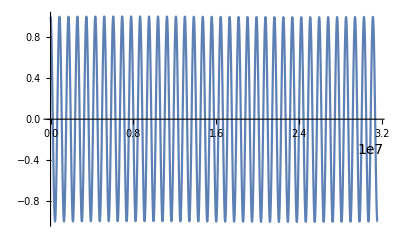

```mathematica
Module[{c=2.99792458*10^8,v=2.9802*10^4,ωe=1.992*10^-7,ω0=(2π)/(3600 24 10)},
γ[v_]:=1/(√(1-(v/c)^2));
β[v_]:=v/c;
Δ[β_]:=√((1-β)/(1+β));
Plot[{BesselJ[0,(ω0 γ[v]β[v])/ωe]Cos[ω0 γ[v]t]+2∑_(n=1)^10 BesselJ[n,(ω0 γ[v]β[v])/ωe]Cos[n ωe t-(n π)/2]},{t,0,(2π)/ωe}]
]
```

What did this exercise teach me?  When the frequence of the GW wave is small we need to take a lot of data to find it, which means we may have to factor in the frequency modulation due to the earth’s motion around the sun.  However the modulation index depends on the frequency we are trying to measure, and it is very small when the frequency is low.  In the case when the frequency is high, we don’t need to take as much data, so the frequency modulation due to the Earth’s motion could be neglected.  In short, I don’t believe using the Gustafson algorithm is necessary in ether case.  So what’s going on here?

```mathematica
Plot[{Cos[ω0 γ[v]t+ω0(γ[v]β[v])/ωe Cos[ωe t]]},{t,0,(2π)/ωe}]
```

When does the modulation factor become significant?  Well, plug in the max value for t, and eliminate the cos’s

```mathematica
ω0 γ[v]((2π)/ωe)+ω0(γ[v]β[v])/ωe
```

pull out constants from both terms

```mathematica
(ω0 γ[v])/ωe(2π+β[v])
```

So apparently it is when β becomes comparable to 2π in magnitude.  Or equivalently in the relativistic regeme.

Alternatively this algorithm could be used to demodulate the frequency of objects that are moving relative to the earth around some binary, but any object moving (accelerating) at speeds where relativity will be taking over is most likely intensly radating gravitational wave radation, and therefore rapidly losing energy.  This means the carrier frequency will drift quickly rendering this algorithm ineffective at picking up the signal.  Basically this isn’t going to find anything.  The only things we could possibly hope to find with this is something moving relativistically and with such increadible mass, that even though it is radating massive ammounts of energy, it is insignificant comparred to the total energy it will have to radiate inorder to merge.

### Folding and Aliasing

```mathematica
Manipulate[
Show[
ListLinePlot[Table[Sin[2π f t],{t,0,5,0.5}],DataRange->{0,5},PlotStyle->Red,PlotMarkers->{●,8},PlotRange->{-1,1}],
Plot[Sin[2π f t],{t,0,5},PlotRange->{-1,1}]
],
{f,0,10,0.1}]
```